```mathematica
a=({{2, 3, -1, 0}, {-6, -5, 0, 2}, {2, -5, 6, -6}, {4, 6, 2, -3}})
```

{{2,3,-1,0},{-6,-5,0,2},{2,-5,6,-6},{4,6,2,-3}}

```mathematica
x=({{x1}, {x2}, {x3}, {x4}})
```

{{x1},{x2},{x3},{x4}}

```mathematica
b=({{20}, {-45}, {-3}, {58}})
```

{{20},{-45},{-3},{58}}

```mathematica
Solve[a.x==b]
```

{{x1→1,x2→7,x3→3,x4→-2}}

```mathematica
QRDecomposition[a]
```

{{{1/(√15),-√(3/5),1/(√15),2/(√15)},{1/(√30),0,-√(5/6),√(2/15)},{-7/(√1130),9 √(2/565),9/(√1130),13 √(2/565)},{-22/(√565),-8/(√565),-4/(√565),1/(√565)}},{{2 √15,-√(5/3)+2 √15,3 √(3/5),-6 √(3/5)},{0,4 √(10/3),2 √(2/15)-1/(√30)-√30,-√(6/5)+√30},{0,0,√(113/10),-48 √(2/565)},{0,0,0,√(5/113)}}}

```mathematica
Map[MatrixForm,%]
```

{(1/(√15) | -√(3/5) | 1/(√15) | 2/(√15)
1/(√30) | 0 | -√(5/6) | √(2/15)
-7/(√1130) | 9 √(2/565) | 9/(√1130) | 13 √(2/565)
-22/(√565) | -8/(√565) | -4/(√565) | 1/(√565)),(2 √15 | -√(5/3)+2 √15 | 3 √(3/5) | -6 √(3/5)
0 | 4 √(10/3) | 2 √(2/15)-1/(√30)-√30 | -√(6/5)+√30
0 | 0 | √(113/10) | -48 √(2/565)
0 | 0 | 0 | √(5/113))}

```mathematica
-1/2(98)+9
```

-40

```mathematica
-1/2(9998)+103
```

-4896

```mathematica
-1/2(10100)+114
```

-4936

```mathematica
-1/4(98)+1
```

-47/2

```mathematica
-1/4(9998)+1
```

-4997/2

```mathematica
-1/4(10100)+3
```

-2522

```mathematica
40/98(98)-40
```

0

```mathematica
40/98(9998)-4896
```

-39944/49

```mathematica
40/98(10100)-4936
```

-39864/49

```mathematica
2*(47/2)(98)-47/2
```

9165/2

```mathematica
Solve[98*x-47/2==0,x]
```

{{x→47/196}}

```mathematica
98(47/196)-47/2
```

0

```mathematica
9998(47/196)-4997/2
```

-4950/49

```mathematica
10100(47/196)-39864/49
```

78811/49

```mathematica
78811/4950
```

78811/4950

```mathematica
Simplify[∑_(v=1)^(m-1) (m-v)^2]
```

1/6 m (1-3 m+2 m^2)

```mathematica
(3/4)^2/(15/4)
```

3/20

```mathematica
15/4-3/20
```

18/5

```mathematica
a=({{4, 1, 1}, {1, 4, 1}, {1, 1, 4}})
```

{{4,1,1},{1,4,1},{1,1,4}}

```mathematica
CholeskyDecomposition[a]
```

{{2,1/2,1/2},{0,(√15)/2,(√(3/5))/2},{0,0,3 √(2/5)}}

```mathematica
%//MatrixForm
```

(2 | 1/2 | 1/2
0 | (√15)/2 | (√(3/5))/2
0 | 0 | 3 √(2/5))

```mathematica
b=({{4, -2, 8, -4}, {-2, 10, -1, 2}, {8, -1, 18, -7}, {-4, 2, -7, 9}})
```

{{4,-2,8,-4},{-2,10,-1,2},{8,-1,18,-7},{-4,2,-7,9}}

```mathematica
CholeskyDecomposition[b]//MatrixForm
```

(2 | -1 | 4 | -2
0 | 3 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 2)

```mathematica
gg[n_,x_]:=∫_0^x g[n,t]ⅆt
```

```mathematica
g[n_,t_]:=Piecewise[{{t^n, 0≤t≤1}, {1, 1≤t≤2}}]
```

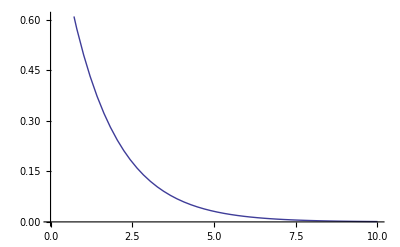

```mathematica
Plot[g[n,0.5],{n,0,10}]
```

```mathematica
gg[0.00001,0.001]
```

0.0999967

```mathematica
gg[100000,100]
```

100002/100001

```mathematica
Limit[gg[n,2],n->∞]
```

1

```mathematica
Limit[1/(n+1)1^(n+1)-1,n->∞]
```

-1

```mathematica
l1=({{1, 0, 0, 0}, {2, 1, 0, 0}, {-1, 0, 1, 0}, {3, 0, 0, 1}})
```

{{1,0,0,0},{2,1,0,0},{-1,0,1,0},{3,0,0,1}}

```mathematica
l2=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, -2, 1, 0}, {0, -1, 0, 1}})
```

{{1,0,0,0},{0,1,0,0},{0,-2,1,0},{0,-1,0,1}}

```mathematica
l3=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 1, 1}})
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,1,1}}

```mathematica
l1.l2.l3//MatrixForm
```

(1 | 0 | 0 | 0
2 | 1 | 0 | 0
-1 | -2 | 1 | 0
3 | -1 | 1 | 1)

```mathematica
l=l1.l2.l3
```

{{1,0,0,0},{2,1,0,0},{-1,-2,1,0},{3,-1,1,1}}

```mathematica
r=({{2, -1, 3, 0}, {0, 3, -3, 1}, {0, 0, -4, 2}, {0, 0, 0, 5}})
```

{{2,-1,3,0},{0,3,-3,1},{0,0,-4,2},{0,0,0,5}}

```mathematica
a=l.r//MatrixForm
```

(2 | -1 | 3 | 0
4 | 1 | 3 | 1
-2 | -5 | -1 | 0
6 | -6 | 8 | 6)

```mathematica
x=({{x1}, {x2}, {x3}, {x4}})
```

{{x1},{x2},{x3},{x4}}

```mathematica
b=({{5}, {10}, {1}, {36}})
```

{{5},{10},{1},{36}}

```mathematica
Solve[l.r.x==b]
```

{{x1→2,x2→-1,x3→0,x4→3}}

```mathematica
Inverse[l].b//MatrixForm
```

(5
0
6
15)

```mathematica
Clear[a,b,c,l,l1,l2,l3]
```

```mathematica
l1=({{1, 0, 0, 0}, {2/3, 1, 0, 0}, {-1/3, 0, 1, 0}, {1/3, 0, 0, 1}})
```

{{1,0,0,0},{2/3,1,0,0},{-1/3,0,1,0},{1/3,0,0,1}}

```mathematica
b=({{36}, {10}, {1}, {5}})
```

{{36},{10},{1},{5}}

```mathematica
l1.b//MatrixForm
```

(36
34
-11
17)

```mathematica
r1=({{6, -6, 8, 6}, {4, 1, 8, 1}, {-2, -5, -1, 0}, {6, -6, 8, 6}})
```

{{6,-6,8,6},{4,1,8,1},{-2,-5,-1,0},{6,-6,8,6}}

```mathematica
l1.r1//MatrixForm
```

(6 | -6 | 8 | 6
8 | -3 | 40/3 | 5
-4 | -3 | -11/3 | -2
12 | -12 | 16 | 12)

```mathematica
8*(-2/3)+8
```

8/3

```mathematica
6*(-2/3)+1
```

-3

```mathematica
-6(1/3)-5
```

-7

```mathematica
8(1/3)-1
```

5/3

```mathematica
6(-1/3)
```

-2

```mathematica
-6(-1)-6
```

0

```mathematica
8(-1)+8
```

0

```mathematica
6(-1/3)+2
```

0

```mathematica
-6(-1/3)-1
```

1

```mathematica
8(-1/3)+3
```

1/3

```mathematica
6(-1/3)+0
```

-2

```mathematica
l2=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, -5/7, 1, 0}, {0, -1/7, 0, 1}})
```

{{1,0,0,0},{0,1,0,0},{0,-5/7,1,0},{0,-1/7,0,1}}

```mathematica
l2.({{36}, {-11}, {34}, {17}})//MatrixForm
```

(36
-11
293/7
130/7)

```mathematica
5/3(5/7)+8/3
```

27/7

```mathematica
5/3(5/7)+1/3
```

32/21

```mathematica
-2(5/7)-3
```

-31/7

```mathematica
Solve[27/7(xx)+1/3==0,xx]
```

{{xx→-7/81}}

```mathematica
l3=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 7/81, 1}})
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,7/81,1}}

```mathematica
l3.({{36}, {-11}, {293/7}, {130/7}})//MatrixForm
```

(36
-11
293/7
12581/567)

```mathematica
-31/7(-7/81)-2
```

-131/81

```mathematica
Solve[-131/81(xxx)==12582/567,xxx]
```

{{xxx→-12582/917}}

```mathematica
%//N
```

{{xxx→-13.7208}}

```mathematica
Clear[a]
```

```mathematica
a=({{4, -2, 8, -4}, {-2, 10, -1, 2}, {8, -1, 18, -7}, {-4, 2, -7, 9}})
```

{{4,-2,8,-4},{-2,10,-1,2},{8,-1,18,-7},{-4,2,-7,9}}

```mathematica
CholeskyDecomposition[a]//MatrixForm
```

(2 | -1 | 4 | -2
0 | 3 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 2)

```mathematica
ConjugateTranspose[%]//MatrixForm
```

(2 | 0 | 0 | 0
-1 | 3 | 0 | 0
4 | 1 | 1 | 0
-2 | 0 | 1 | 2)

```mathematica
a3=({{10, -1, 2}, {-1, 18, -7}, {2, -7, 9}})-1/4*({{-2}, {8}, {-4}}).ConjugateTranspose[({{-2}, {8}, {-4}})]//MatrixForm
```

(9 | 3 | 0
3 | 2 | 1
0 | 1 | 5)

```mathematica
Solve[a.x==({{0}, {0}, {0}, {1}})]
```

{{x1→19/24,x2→1/12,x3→-1/4,x4→1/4}}

```mathematica
-3/2-2
```

-7/2

```mathematica
(9/2)/4
```

9/8

```mathematica
-9/8-7/2
```

-37/8

```mathematica
37/8-3/2
```

25/8

```mathematica
%/3
```

25/24

```mathematica
3/2+1/2
```

2

```mathematica
37/8+1
```

45/8

```mathematica
9/8+2
```

25/8

```mathematica
2*37/8+25/8
```

99/8

```mathematica
1/6(9/2+3/2+9/2+3/2)
```

2

```mathematica
({{3/2}, {1/2}, {-3/2}, {1/2}})-2/6({{3}, {3}, {-3}, {3}})//MatrixForm
```

(1/2
-1/2
-1/2
-1/2)

```mathematica
Norm[({{1/2}, {-1/2}, {-1/2}, {-1/2}})]
```

1

```mathematica
1/6(-7*3-12+9)
```

-4

```mathematica
1/√2(-7-4)
```

-11/(√2)

```mathematica
({{-7}, {0}, {4}, {3}})+4/6({{3}, {3}, {-3}, {3}})+7({{1/2}, {-1/2}, {-1/2}, {-1/2}})//MatrixForm
```

(-3/2
-3/2
-3/2
3/2)

```mathematica
Norm[({{-3/2}, {-3/2}, {-3/2}, {3/2}})]
```

3

```mathematica
Clear[a]
```

```mathematica
a=({{3, 3/2, -7, 5}, {3, 1/2, 0, -2}, {-3, -3/2, 4, -3}, {3, 1/2, 3, 4}})
```

{{3,3/2,-7,5},{3,1/2,0,-2},{-3,-3/2,4,-3},{3,1/2,3,4}}

```mathematica
QRDecomposition[a]
```

{{{1/2,1/2,-1/2,1/2},{1/2,-1/2,-1/2,-1/2},{-1/2,-1/2,-1/2,1/2},{1/2,-1/2,1/2,1/2}},{{6,2,-4,5},{0,1,-7,3},{0,0,3,2},{0,0,0,4}}}

```mathematica
Map[MatrixForm,%]
```

{(1/2 | 1/2 | -1/2 | 1/2
1/2 | -1/2 | -1/2 | -1/2
-1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2),(6 | 2 | -4 | 5
0 | 1 | -7 | 3
0 | 0 | 3 | 2
0 | 0 | 0 | 4)}

```mathematica
-7*(1/2)-2-3/2
```

-7

```mathematica
1/6(15-6+9+12)
```

5

```mathematica
5/2+1+3/2-2
```

3

```mathematica
-5/2+1+3/2+2
```

2

```mathematica
({{5}, {-2}, {-3}, {4}})-5/6({{3}, {3}, {-3}, {3}})-3({{1/2}, {-1/2}, {-1/2}, {-1/2}})-2({{-1/2}, {-1/2}, {-1/2}, {1/2}})
```

{{2},{-2},{2},{2}}

```mathematica
Norm[%]
```

4

```mathematica
1/6(9/2+3/2+9/2+3/2)
```

2

```mathematica
1/6(-21-12+9)
```

-4

```mathematica
-7/2-2-3/2
```

-7

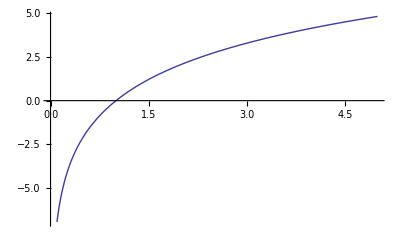

```mathematica
Plot[Log[x^3],{x,0,5}]
```

```mathematica
Log[1]
```

0

```mathematica
mk={229400,67900,162000,57100,62300,16900,7700,5000,3000,10000,3000}
```

{229400,67900,162000,57100,62300,16900,7700,5000,3000,10000,3000}

```mathematica
mh={2035.3,1217.8,436,436,289.1,76,50.4,68.6,45.6,84.3,68.6}
```

{2035.3,1217.8,436,436,289.1,76,50.4,68.6,45.6,84.3,68.6}

```mathematica
mklog=Log@mk//N
```

{12.3432,11.1258,11.9954,10.9526,11.0397,9.73507,8.94898,8.51719,8.00637,9.21034,8.00637}

```mathematica
mhlog=Log@mh//N
```

{7.6184,7.1048,6.07764,6.07764,5.66677,4.33073,3.91999,4.22829,3.81991,4.43438,4.22829}

```mathematica
Total[mklog]
```

109.881

```mathematica
(#^2&)@mklog
```

{152.355,123.783,143.888,119.959,121.875,94.7716,80.0842,72.5426,64.1019,84.8304,64.1019}

```mathematica
Total[(#^2&)@mklog]
```

1122.29

```mathematica
Total[mhlog]
```

57.5069

```mathematica
mklog.Transpose[mhlog]
```

Transpose::nmtx: The first two levels of the one-dimensional list {7.6184, 7.1048, 6.07764, 6.07764, 5.66677, 4.33073, 3.91999, 4.22829, 3.81991, 4.43438, 4.22829} cannot be transposed.

{12.3432,11.1258,11.9954,10.9526,11.0397,9.73507,8.94898,8.51719,8.00637,9.21034,8.00637}.Transpose[{7.6184,7.1048,6.07764,6.07764,5.66677,4.33073,3.91999,4.22829,3.81991,4.43438,4.22829}]

```mathematica
mklog//MatrixForm
```

(12.3432
11.1258
11.9954
10.9526
11.0397
9.73507
8.94898
8.51719
8.00637
9.21034
8.00637)

```mathematica
mhlog//MatrixForm
```

(7.6184
7.1048
6.07764
6.07764
5.66677
4.33073
3.91999
4.22829
3.81991
4.43438
4.22829)

```mathematica
mklog.mhlog
```

593.643

```mathematica
Solve[({{11, 109.881}, {109.881, 1122.29}}).({{α}, {β}})==({{57.5069}, {593.643}})]
```

{{α→-2.54525,β→0.778157}}

```mathematica
Plot[f[x]:=-2.54525+0.778157x,{x,0,10}]
```

-Graphics-

```mathematica
f[x_]:=-2.54525+0.778157x
```

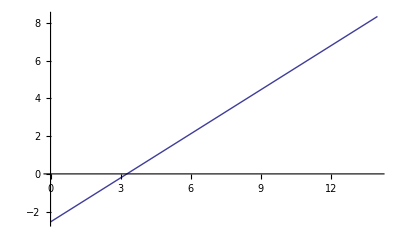

```mathematica
Plot[f[x],{x,0,14}]
```

```mathematica
2035.3^2.5
```

1.86884×10^8

```mathematica
%//N
```

1.86884×10^8

```mathematica
pair=Thread[{mklog,mhlog}]
```

{{12.3432,7.6184},{11.1258,7.1048},{11.9954,6.07764},{10.9526,6.07764},{11.0397,5.66677},{9.73507,4.33073},{8.94898,3.91999},{8.51719,4.22829},{8.00637,3.81991},{9.21034,4.43438},{8.00637,4.22829}}

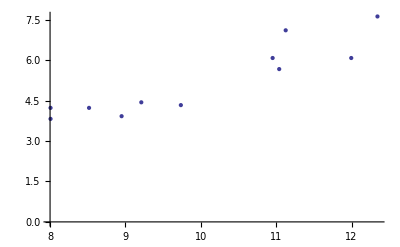

```mathematica
ListPlot[pair]
```

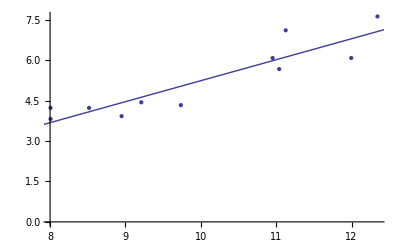

```mathematica
Show[ListPlot[pair],Plot[f[x],{x,0,14}]]
```

```mathematica
Solve[({{11, 109.881}, {109.881, 1122.29}}).({{α}, {β}})==({{57.5069}, {593.643}})]
```

{{α→-2.54525,β→0.778157}}

```mathematica
Solve[1122.29β==593.643]
```

{{β→0.528957}}

```mathematica
Solve[109.881β==57.5069]
```

{{β→0.523356}}

```mathematica
Solve[Log[mh[[1]]]==α Log[mk[[1]]]]
```

{{α→0.617213}}

```mathematica
Table[Solve[Log[mh[[n]]]==α Log[mk[[n]]]],{n,1,11}]//N
```

{{{α→0.617213}},{{α→0.638588}},{{α→0.506666}},{{α→0.554906}},{{α→0.513308}},{{α→0.444859}},{{α→0.438038}},{{α→0.496442}},{{α→0.477109}},{{α→0.481457}},{{α→0.528116}}}

```mathematica
g[x_]:=0.53x
```

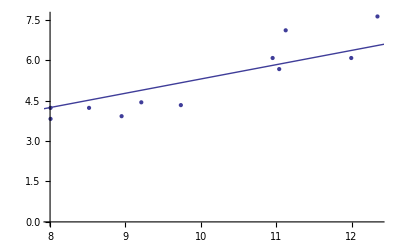

```mathematica
Show[ListPlot[pair],Plot[g[x],{x,0,14}]]
```

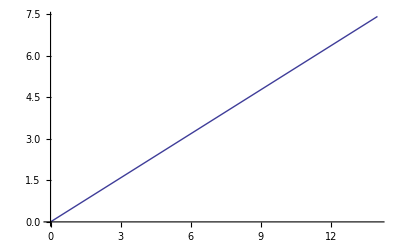

```mathematica
Plot[g[x],{x,0,14}]
```